# EWPT of the VDDMM

## Loading package and Feynman rules

```mathematica
NotebookEvaluate["/home/bastilo/Dropbox/ProyectoVectorDM/ObliqueParameters/New/DefinicionesV2.nb"];
Options[OneLoop];
```

Loading FeynCalc from /home/bastilo/.Mathematica/Applications/HighEnergyPhysics

HighEnergyPhysics`FeynCalc`MemoryAvailable`MemoryAvailable::shdw: Symbol MemoryAvailable appears in multiple contexts {HighEnergyPhysics`FeynCalc`MemoryAvailable`,System`}; definitions in context HighEnergyPhysics`FeynCalc`MemoryAvailable` may shadow or be shadowed by other definitions.

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading PHI

WARNING! Your FeynArts installation is not complete or the version you have cannot be used with this version of FeynCalc.
FeynArts can be downloaded at www.feynarts.de

Loading FeynArts, see www.feynarts.de for documentation

FeynArts not found. Please install FeynArts, e.g., in
/home/bastilo/.Mathematica
and reload FeynCalc
FeynArts can be downloaded from www.feynarts.de

```mathematica
Install["/home/bastilo/Documents/Programas/LoopTools-2.15/x86_64-Linux/bin/LoopTools"];
```

PaVe::shdw: Symbol PaVe appears in multiple contexts {LoopTools`,HighEnergyPhysics`fcloops`PaVe`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

Li2::shdw: Symbol Li2 appears in multiple contexts {LoopTools`,HighEnergyPhysics`FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

A0::shdw: Symbol A0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`A0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B0::shdw: Symbol B0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B1::shdw: Symbol B1 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B1`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B00::shdw: Symbol B00 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B00`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B11::shdw: Symbol B11 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B11`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB0::shdw: Symbol DB0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`DB0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB1::shdw: Symbol DB1 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`DB1`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

C0::shdw: Symbol C0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`C0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

D0::shdw: Symbol D0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`D0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

## Vaccum polarization Amplitudes

WW-polarization

```mathematica
-Graphics- + -Graphics- +-Graphics- +-Graphics-;
```

## Amplitudes

```mathematica
MWW1=Contract[WVCV1[-q,q-l,l,μ,a,d].propVC[q-l,b,a].WVCV1[q,-q+l,-l,ν,b,s].propV1[l,s,d]];
MWW1L=OneLoop[l,%];
MWW1LPV=Simplify[PaVeReduce[MWW1L]];

MWW2=Contract[WVCV2b[-q,q-l,l,μ,a,d].propVC[q-l,b,a].WVCV2a[q,-q+l,-l,ν,b,s].propV2[l,d,s]];
MWW2L=OneLoop[l,%];
MWW2LPV=Simplify[PaVeReduce[MWW2L]];

MWW3=Contract[WWVCVC[μ,ν,α,β].propVC[q-l,α,β]];
MWW3L=OneLoop[l,%];
MWW3LPV=Simplify[PaVeReduce[MWW3L]];

MWW41=Contract[WWV1V1[μ,ν,α,β].propV1[q-l,α,β]];
MWW41L=OneLoop[l,%];
MWW41LPV=Simplify[PaVeReduce[MWW41L]];

MWW42=Contract[WWV2V2[μ,ν,α,β].propV2[q-l,α,β]];
MWW42L=OneLoop[l,%];
MWW42LPV=Simplify[PaVeReduce[MWW42L]];
```

## Sum of amplitudes

```mathematica
MWW=I/(64*π^4)Simplify[MWW1LPV+MWW2LPV+MWW3LPV+MWW41LPV+MWW42LPV];
ScalarProduct[FV[y,μ],FV[y,μ]]=1;
ScalarProduct[FV[q,μ],FV[y,μ]]=0;
ScalarProduct[y,y]=1;
ScalarProduct[q,y]=0;
```

## Getting the term proportional to gmunu

```mathematica
ΠWW=Expand[Contract[MWW,FV[y,μ].FV[y,ν]]];
ΠWWx=ΠWW/.ScalarProduct[q,q]->x;
```

## Replacing A0 to B0 and expanding B0(x,m1,m2)

```mathematica
(*SetOptions[A0,A0ToB0->True];
```

```mathematica
BB12=Normal[Series[B0[x,MV1^2,MV2^2],{x,0,1}]];
BB1C=Normal[Series[B0[x,MV1^2,MVC^2],{x,0,1}]];
BB2C=Normal[Series[B0[x,MV2^2,MVC^2],{x,0,1}]];
```

## The amplitude after replacements

```mathematica
WWF=Simplify[ΠWWx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
WW0=Expand[WWF]/.{x->0};
```

ZZ-polarization

## -Graphics-+-Graphics-+-Graphics-+-Graphics-

## Amplitudes

```mathematica
MZZ1=Contract[ZVCVC[-q,q-l,l,μ,a,d].propVC[q-l,b,a].ZVCVC[q,-l,-q+l,ν,s,b].propVC[l,s,d]];
MZZ1L=OneLoop[l,%];
MZZ1LPV=Simplify[PaVeReduce[MZZ1L]];

MZZ2=Contract[ZV1V2[-q,l,q-l,μ,d,a].propV2[q-l,b,a].ZV1V2[q,-l,-q+l,ν,s,b].propV1[l,d,s]];
MZZ2L=OneLoop[l,%];
MZZ2LPV=Simplify[PaVeReduce[MZZ2L]];

MZZ3=Contract[ZZVCVC[μ,ν,α,β].propVC[q-l,α,β]];
MZZ3L=OneLoop[l,%];
MZZ3LPV=Simplify[PaVeReduce[MZZ3L]];

MZZ41=Contract[ZZV1V1[μ,ν,α,β].propV1[q-l,α,β]];
MZZ41L=OneLoop[l,%];
MZZ41LPV=Simplify[PaVeReduce[MZZ41L]];

MZZ42=Contract[ZZV2V2[μ,ν,α,β].propV2[q-l,α,β]];
MZZ42L=OneLoop[l,%];
MZZ42LPV=Simplify[PaVeReduce[MZZ42L]];
```

## Sum of amplitudes

```mathematica
MZZ=I/(64*π^4)Simplify[MZZ1LPV+MZZ2LPV+MZZ3LPV+MZZ41LPV+MZZ42LPV];
ScalarProduct[FV[y,μ],FV[y,μ]]=1;
ScalarProduct[FV[q,μ],FV[y,μ]]=0;
ScalarProduct[y,y]=1;
ScalarProduct[q,y]=0;
```

Set::setraw: Cannot assign to raw object 1.

## Getting the term proportional to gmunu

```mathematica
ΠZZ=Expand[Contract[MZZ,FV[y,μ].FV[y,ν]]];
ΠZZx=ΠZZ/.ScalarProduct[q,q]->x;
```

## The amplitude after replacements

```mathematica
ZZF=Simplify[ΠZZx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
ZZMZ=Expand[ZZF]/.{x->MZ^2};
ZZ0=Expand[ZZF]/.{x->0};
```

```mathematica
(*SetOptions[A0,A0ToB0->False];
```

Zγ-Amplitude polarization

```mathematica
MZγ=Contract[AZVCVC[μ,ν,α,β].propVC[q-l,α,β]];
MZγL=OneLoop[l,%];
MZγLPV=I/(64*π^4)Simplify[PaVeReduce[MZγL]];
```

## Getting the term proportional to gmunu

```mathematica
ΠZγ=Contract[MZγLPV,FV[y,μ].FV[y,ν]];
ΠZγx=ΠZγ/.ScalarProduct[q,q]->x;
```

## Expanding some amplitudes and replacing q^2->MZ^2

```mathematica
ZγF=Simplify[ΠZγx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
ZγMZ=Expand[ZγF]/.{x->MZ^2};
```

γγ-Amplitude

```mathematica
-Graphics--Graphics-
```

```mathematica
Mγγ1=Contract[AVCVC[-q,q-l,l,μ,a,d].propVC[q-l,b,a].AVCVC[q,-l,-q+l,ν,s,b].propVC[l,s,d]];
Mγγ1L=OneLoop[l,%];
Mγγ1LPV=Simplify[PaVeReduce[Mγγ1L]];

Mγγ2=Contract[AAVCVC[μ,ν,α,β].propVC[q-l,α,β]];
Mγγ2L=OneLoop[l,%];
Mγγ2LPV=Simplify[PaVeReduce[Mγγ2L]];

MγγLPV=I/(64*π^4)Simplify[Mγγ1LPV+Mγγ2LPV];
```

## Getting the term proportional to gmunu

```mathematica
Πγγ=Contract[MγγLPV,FV[y,μ].FV[y,ν]];
Πγγx=Πγγ/.ScalarProduct[q,q]->x;
```

## Expanding some amplitudes and replacing q^2->MZ^2

```mathematica
γγF=Simplify[Πγγx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
γγMZ=Expand[γγF]/.{x->MZ^2};
```

T-parameter

```mathematica
T1=(WW0/(cw*MZ)^2-ZZ0/MZ^2)/α;
```

```mathematica
(*Pag. 70 One-Loop Romao. DB0 were calculated with Mathematica*)
Repμ:={
A0[MV1^2]->(MV1^2)(Δ+1-Log[MV1^2/μ^2]),
A0[MV2^2]->(MV2^2)(Δ+1-Log[MV2^2]/μ^2),
A0[MVC^2]->(MVC^2)(Δ+1-Log[MVC^2]/μ^2),
B0[0,MV1^2,MV2^2]->Δ+1-(MV1^2Log[MV1^2]-MV2^2Log[MV2^2])/(MV1^2-MV2^2),
B0[0,MV1^2,MVC^2]->Δ+1-(MV1^2Log[MV1^2]-MVC^2Log[MVC^2])/(MV1^2-MVC^2),
B0[0,MV2^2,MVC^2]->Δ+1-(MV2^2Log[MV2^2]-MVC^2Log[MVC^2])/(MV2^2-MVC^2),
B0[0,MV1^2,MV1^2]->Δ-Log[MV1^2/μ^2],
B0[0,MV2^2,MV2^2]->Δ-Log[MV2^2/μ^2],
B0[0,MVC^2,MVC^2]->Δ-Log[MVC^2/μ^2],
DB0[0,MV1^2,MV2^2]->-(MV1^4-MV2^4-2 MV1^2 MV2^2 Log[MV1^2/MV2^2])/(2 (MV1^2-MV2^2)^3),
DB0[0,MV1^2,MVC^2]->-(MV1^4-MVC^4-2 MV1^2 MVC^2 Log[MV1^2/MVC^2])/(2 (MV1^2-MVC^2)^3),
DB0[0,MV2^2,MVC^2]->-(MV2^4-MVC^4-2 MV2^2 MVC^2 Log[MV2^2/MVC^2])/(2 (MV2^2-MVC^2)^3),
B0[MZ^2,MVC^2,MVC^2]->Δ-Log[MVC^2/μ^2]-(2 √(4*MVC^2-MZ^2)ArcTan[MZ/(√(4*MVC^2-MZ^2))])/MZ+2
};
```

The T parameter with Repμ

```mathematica
T2=T1/.Repμ/.{α->e^2/(4π)};//Simplify;
```

The expansion of the T parameter in Δ

```mathematica
T3a=Series[T2,{Δ,0,1}]//Simplify;
T3b=Series[T2,{Δ,0,0}]//Simplify;
```

```mathematica
(*NumT3b=Numerator[Normal[T3b]]
NumT3b/.{MV2->MVC};
```

Replacement  Δ -> Log[Λ^2/μ^2]  and   Δ -> Log[Λ^2/μ^2] -1

```mathematica
T30=Normal[T2]/.{Δ->Log[Λ^2/μ^2]};
T31=Normal[T2]/.{Δ->Log[Λ^2/μ^2]-1};
```

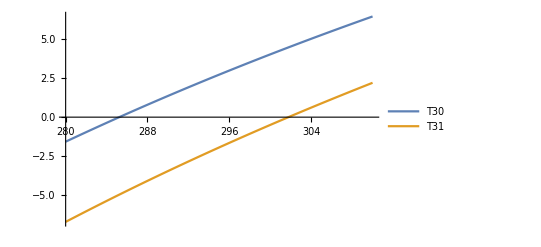

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ,μ},
MV2=400;
MVC=605;
sw=0.4;
cw=√(1-sw^2);
MZ=91.1;
Λ=2000;
μ=MZ;
Plot[{T30,T31},{MV1,280,310},PlotLegends->"Expressions"]]
```

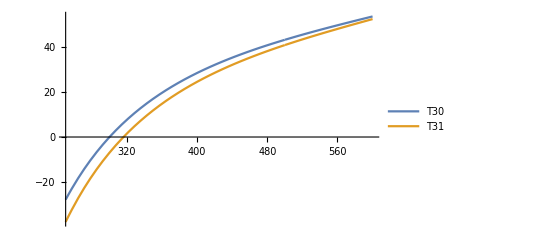

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ,μ,α},
α=1;
MV2=500;
MVC=700;
sw=0.4;
cw=√(1-sw^2);
MZ=91.1;
Λ=2000;
μ=MZ;
Plot[{T30,T31},{MV1,250,600},PlotLegends->"Expressions"]]
```

S-parameter

```mathematica
Clear[S1]
Clear[S2]
Clear[S30]
Clear[S31]
```

```mathematica
S1=(4*cw^2*sw^2)/α((ZZMZ - ZZ0)/MZ^2-(cw^2-sw^2)/(cw*sw)ZγMZ/MZ^2-γγMZ/MZ^2);
S2=S1/.Repμ/.{α->e^2/(4π)}//Simplify;
```

## Replacing the Δ -> Log

```mathematica
S30=Normal[S2]/.{Δ->Log[Λ^2/μ^2]}//Simplify;
S31=Normal[S2]/.{Δ->Log[Λ^2/μ^2]-1}//Simplify;
```

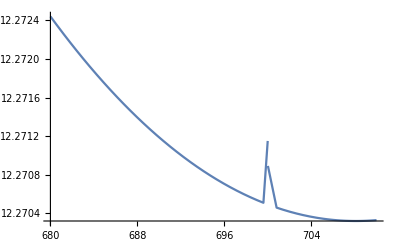

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ,μ,e},
e=8.5*10^-2;
MV2=700;
MVC=805;
sw=0.4;
cw=√(1-sw^2);
MZ=91;
Λ=2000;
μ=200;
Plot[{S31},{MV1,680,710},PlotLegends->"Expressions"]]
```

## Trush

Pauli-Villars

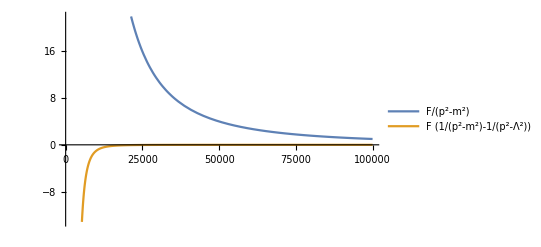

```mathematica
Block[{m,Λ,F},F=10^10;m=1;Λ=10^3;
Plot[{F*(1/(p^2-m^2)),F*(1/(p^2-m^2)-1/(p^2-Λ^2))},{p,0,10^5},PlotLegends->"Expressions"]]
```

```mathematica
Block[{MZ,μ,MVC},∫_0^1 Log[(-x*(1-x)*MZ^2+MVC^2)/μ^2]ⅆx]
```